This documentation describes simulation particle loading along the central mirror field line.

## Non-Relativistic Particle Loading

According to Liouville's theorem, the phase space density, f(𝕧,𝕣), is constant along the characteristic path.
By virtue of conservation of total energy (ε=(m v^2)/2) and first adiabatic moment (μ=(m v_⊥^2)/(2B)), 
f(𝕧(ε,μ),𝕣(ε,μ)) is constant of motion, if f is gyrotropic.

Conservation of μ:
(v_⊥^2)/B=(v_(⊥,0)^2)/B_0 → v_(⊥,0)^2=B_0/B v_⊥^2, 
where subscript 0 denotes quantities at the origin.

Conservation of ε:
v_∥^2+v_⊥^2=v_(∥,0)^2+v_(⊥,0)^2 → v_(∥,0)^2=v_∥^2+v_⊥^2-v_(⊥0)^2=v_∥^2+(1-B_0/B)v_⊥^2.

### Bi-Maxwellian velocity distribution

Consider a bi-Maxwellian velocity distribution at the origin
f_0[v_(∥,0),v_(⊥,0)]=n_0(ⅇ^(-v_(∥,0)^2/θ_(∥,0)^2))/(√π θ_(∥,0))(ⅇ^(-v_(⊥,0)^2/θ_(⊥,0)^2))/(π θ_(⊥,0)^2).
Substituting v_(∥,0)(v_∥,v_⊥) and v_(⊥,0)(v_∥,v_⊥) from above, the distribution at a given location can be obtained from
f[v_∥,v_⊥]=f_0[√(v_∥^2+(1-B_0/B)v_⊥^2),√(B_0/B)v_⊥]
=n_0 1/(√π θ_(∥,0))1/(π θ_(⊥,0)^2)Exp[-(v_∥^2+(1-B_0/B)v_⊥^2)/(θ_(∥,0)^2)]Exp[-B_0/B(v_⊥^2)/(θ_(⊥,0)^2)]
=n_0 1/(√π θ_(∥,0))1/(π θ_(⊥,0)^2)Exp[-(v_∥^2)/(θ_(∥,0)^2)-(1-B_0/B)(v_⊥^2)/(θ_(∥,0)^2)]Exp[-B_0/B(v_⊥^2)/(θ_(⊥,0)^2)]
=n_0 1/(√π θ_(∥,0))1/(π θ_(⊥,0)^2)Exp[-(v_∥^2)/(θ_(∥,0)^2)]Exp[-(1-B_0/B)(v_⊥^2)/(θ_(∥,0)^2)-B_0/B(v_⊥^2)/(θ_(⊥,0)^2)]
=n_0 1/(√π θ_(∥,0))1/(π θ_(⊥,0)^2)Exp[-(v_∥^2)/(θ_(∥,0)^2)]Exp[-((1-B_0/B)(θ_(⊥,0)^2)/(θ_(∥,0)^2)+B_0/B)(v_⊥^2)/(θ_(⊥,0)^2)].
Expressing it using new thermal speeds 
θ_∥^2=θ_(∥,0)^2 and θ_⊥^2=((1-B_0/B)(θ_(⊥,0)^2)/(θ_(∥,0)^2)+B_0/B)^-1 θ_(⊥,0)^2 
and a new number density 
n=((1-B_0/B)(θ_(⊥,0)^2)/(θ_(∥,0)^2)+B_0/B)^-1 n_0 
yields
f[v_∥,v_⊥]=n 1/(√π θ_∥)1/(π θ_⊥^2)Exp[-(v_∥^2)/(θ_∥^2)]Exp[-(v_⊥^2)/(θ_⊥^2)].
Hence, the distribution at any location along the field line is a bi-Maxwellian with adjusted thermal speeds.
We can write the following macro variables in terms of the ones at origin:
T_∥=T_(∥,0);
T_⊥=((1-B_0/B)(T_(⊥,0))/(T_(∥,0))+B_0/B)^-1 T_(⊥,0);
n=((1-B_0/B)(θ_(⊥,0)^2)/(θ_(∥,0)^2)+B_0/B)^-1 n_0;
P_∥=n T_∥=((1-B_0/B)(θ_(⊥,0)^2)/(θ_(∥,0)^2)+B_0/B)^-1 n_0 T_(∥,0)=((1-B_0/B)(θ_(⊥,0)^2)/(θ_(∥,0)^2)+B_0/B)^-1 P_(∥,0);
P_⊥=n T_⊥=((1-B_0/B)(θ_(⊥,0)^2)/(θ_(∥,0)^2)+B_0/B)^-2 n_0 T_(⊥,0)=((1-B_0/B)(θ_(⊥,0)^2)/(θ_(∥,0)^2)+B_0/B)^-2 P_(⊥,0).

Since we are concerned with the central field line of the mirror magnetic field,
we can substitute (B(x))/B_0=(B_x(x))/B_0=1+ξ^2 x^2=sec^2(ξ Δ_1 q^1) to the common factor:
η=n/n_0=((1-B_0/B)(θ_(⊥,0)^2)/(θ_(∥,0)^2)+B_0/B)^-1=(B/B_0)/(1-(T_(⊥,0))/(T_(∥,0))(1-B/B_0))
=(1+ξ^2 x^2)/(1-(T_(⊥,0)/T_(∥,0))ξ^2 x^2)=(1+ξ^2 x^2)/((1-√(T_(⊥,0)/T_(∥,0))ξ x)(1+√(T_(⊥,0)/T_(∥,0))ξ x))
=(sec^2(ξ Δ_1 q^1))/(1-(T_(⊥,0)/T_(∥,0))(1-sec^2(ξ Δ_1 q^1)))=1/((T_(⊥,0)/T_(∥,0))+(1-(T_(⊥,0)/T_(∥,0)))cos^2(ξ Δ_1 q^1)).
Note that η=1 if ξ=0 or T_(⊥,0)/T_(∥,0)=1.
The number of particles in a differential volume, ⅆV, is given by ⅆN=nⅆV.
Since ⅆV=Δ_1 Δ_2 Δ_3 ⅆ q^1ⅆ q^2ⅆ q^3 is constant in terms of curvilinear coordinates, 
ⅆN∝η(q^1).
Considering a flux tube of ⅆ q^2×ⅆ q^3 wide, the integrated number of particles with respect to q^1 is given by
(N(q^1))/n_0=Δ_1 Δ_2 Δ_3 ⅆ q^2ⅆ q^3∫^(q^1) η(q^1)ⅆ q^1
=Δ_1 Δ_2 Δ_3 ⅆ q^2ⅆ q^3∫_0^(q^1) (ⅆ q^1)/((T_(⊥,0)/T_(∥,0))+(1-(T_(⊥,0)/T_(∥,0)))cos^2(ξ Δ_1 q^1))
=(Δ_2 Δ_3 ⅆ q^2ⅆ q^3)/ξ∫_0^(q^1) (ξ Δ_1 ⅆ q^1)/((T_(⊥,0)/T_(∥,0))+(1-(T_(⊥,0)/T_(∥,0)))cos^2(ξ Δ_1 q^1))
=(Δ_2 Δ_3 ⅆ q^2ⅆ q^3)/ξ(tan^-1(√(T_(⊥,0)/T_(∥,0))tan(ξ Δ_1 q^1)))/(√(T_(⊥,0)/T_(∥,0))),
where N(0)=0.
Note the limiting case lim_(ξ→0) (N(q^1))/n_0=q^1 Δ_1 Δ_2 Δ_3 ⅆ q^2ⅆ q^3.
The inverse relation q^1(N) is given by
q^1(N)=1/(ξ Δ_1)tan^-1(1/(√(T_(⊥,0)/T_(∥,0)))tan((√(T_(⊥,0)/T_(∥,0))ξ)/(Δ_2 Δ_3 ⅆ q^2ⅆ q^3)N/n_0)) 
with the limiting case lim_(ξ→0) (q^1(N))=(N/n_0)/(Δ_1 Δ_2 Δ_3 ⅆ q^2ⅆ q^3).

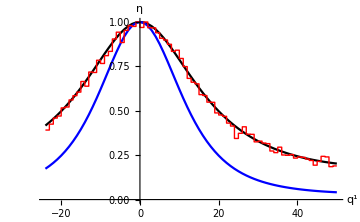
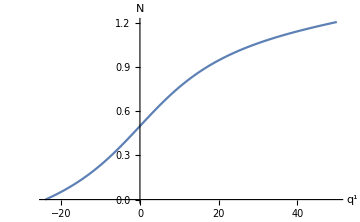

```mathematica
With[{T2OT1=5.35,ξ=.876,q1lim={-24,50},ξΔ1q1max=Pi/2*.8,nsamples=50000},
BlockRandom[
SeedRandom[49038];
Module[{Δ1,q1s,Bs,ηs,xs,Nofq1,tmp,q1ofN,q1samples,bins,hist},
Δ1=Divide[ξΔ1q1max,ξ Max[Abs[q1lim]]];
q1s=Range@@q1lim;
xs=Tan[ξ Δ1 q1s]/ξ;
Bs=Sec[ξ Δ1 q1s]^2;
ηs=Divide[1,T2OT1+(1-T2OT1)Cos[ξ Δ1 q1s]^2];
If[!Apply[And,Thread[0==Chop[ηs-Power[(1-1/Bs)T2OT1+1/Bs,-1]]]],(Print["ηs incorrect"];Abort[])];
Nofq1=ArcTan[√T2OT1 Tan[ξ Δ1 q1s]]/(ξ √T2OT1);
tmp=MinMax[Nofq1]-Map[NIntegrate[Power[T2OT1+(1-T2OT1)Cos[ξ Δ1 q1]^2,-1]Δ1,{q1,0,#}]&,MinMax[q1s]];
If[!Apply[And,Thread[0==Chop[tmp]]],(Print["N(q1) incorrect"];Abort[])];
q1ofN=ArcTan[Tan[√T2OT1 ξ Nofq1]/√T2OT1]/(ξ Δ1);
If[!Apply[And,Thread[Chop[q1s-q1ofN]==0]],(Print["q1(N) incorrect"];Abort[])];
q1samples=ArcTan[Tan[√T2OT1 ξ RandomReal[MinMax[Nofq1],nsamples]]/√T2OT1]/(ξ Δ1);
{bins,hist}=N@HistogramList[q1samples,Append[q1lim,1],"Count"];
bins=Flatten[bins];
Show[#,
ImageSize->Medium
]&/@{
Show[
ListPlot[Thread[{q1s,#}]&/@{ηs,ηs^2},Joined->True,AxesLabel->{"\!\(q^1\)","\!\(η(q^1)\)"},PlotStyle->Thread[Directive[{Black,Blue}]]],
ListStepPlot[Thread[{MovingAverage[bins,2],hist/Max[hist]}],Center,PlotStyle->Directive[Red,Thickness[Medium]]]
],
(*ListPlot[Thread[{xs,#}]&/@{ηs,ηs^2},Joined->True,AxesLabel->{"\!\(x\)","\!\(η(q^1)\)"}],*)
ListPlot[Thread[{q1s,Nofq1-Min[Nofq1]}],Joined->True,AxesLabel->{"\!\(q^1\)","\!\(N(q^1)\)"}]
}
]
]
]
```